```mathematica
Needs["GraphUtilities`"];
```

```mathematica
g={1->2,2->3,3->1,1->4,2->4,3->4,4->5,4->6,4->7,6->1,1->7,7->2,2->5,5->3,3->6}
```

{1→2,2→3,3→1,1→4,2→4,3→4,4→5,4→6,4→7,6→1,1→7,7→2,2→5,5→3,3→6}

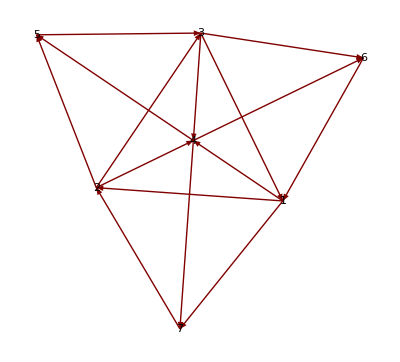

```mathematica
GraphPlot[{1->2,2->3,3->1,1->4,2->4,3->4,4->5,4->6,4->7,6->1,1->7,7->2,2->5,5->3,3->6},VertexLabeling->True,DirectedEdges->True]
```

```mathematica
MatrixForm[AdjacencyMatrix[{1->2,2->3,3->1,1->4,2->4,3->4,4->5,4->6,4->7,6->1,1->7,7->2,2->5,5->3,3->6}]]
```

```mathematica
({{0, 1, 0, 1, 0, 0, 1}, {0, 0, 1, 1, 1, 0, 0}, {1, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 1, 1, 1}, {0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0}})
```

```mathematica
({{0, 1, 0, 1, 0, 0, 1}, {0, 0, 1, 1, 1, 0, 0}, {1, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 1, 1, 1}, {0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0}})
```

```mathematica
Table[MatrixPower[{{0,1,0,1,0,0,1},{0,0,1,1,1,0,0},{1,0,0,1,0,1,0},{0,0,0,0,1,1,1},{0,0,1,0,0,0,0},{1,0,0,0,0,0,0},{0,1,0,0,0,0,0}},i]//MatrixForm,{i,1,25}]
```

{(0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 1 | 1 | 2 | 1 | 1
1 | 0 | 1 | 1 | 1 | 2 | 1
1 | 1 | 0 | 1 | 1 | 1 | 2
1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0),(2 | 1 | 3 | 2 | 2 | 2 | 1
3 | 2 | 1 | 2 | 1 | 2 | 2
1 | 3 | 2 | 2 | 2 | 1 | 2
1 | 1 | 1 | 3 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 2
0 | 1 | 1 | 1 | 2 | 1 | 1
1 | 0 | 1 | 1 | 1 | 2 | 1),(5 | 3 | 3 | 6 | 3 | 5 | 4
3 | 5 | 3 | 6 | 4 | 3 | 5
3 | 3 | 5 | 6 | 5 | 4 | 3
2 | 2 | 2 | 3 | 4 | 4 | 4
1 | 3 | 2 | 2 | 2 | 1 | 2
2 | 1 | 3 | 2 | 2 | 2 | 1
3 | 2 | 1 | 2 | 1 | 2 | 2),(8 | 9 | 6 | 11 | 9 | 9 | 11
6 | 8 | 9 | 11 | 11 | 9 | 9
9 | 6 | 8 | 11 | 9 | 11 | 9
6 | 6 | 6 | 6 | 5 | 5 | 5
3 | 3 | 5 | 6 | 5 | 4 | 3
5 | 3 | 3 | 6 | 3 | 5 | 4
3 | 5 | 3 | 6 | 4 | 3 | 5),(15 | 19 | 18 | 23 | 20 | 17 | 19
18 | 15 | 19 | 23 | 19 | 20 | 17
19 | 18 | 15 | 23 | 17 | 19 | 20
11 | 11 | 11 | 18 | 12 | 12 | 12
9 | 6 | 8 | 11 | 9 | 11 | 9
8 | 9 | 6 | 11 | 9 | 9 | 11
6 | 8 | 9 | 11 | 11 | 9 | 9),(35 | 34 | 39 | 52 | 42 | 41 | 38
39 | 35 | 34 | 52 | 38 | 42 | 41
34 | 39 | 35 | 52 | 41 | 38 | 42
23 | 23 | 23 | 33 | 29 | 29 | 29
19 | 18 | 15 | 23 | 17 | 19 | 20
15 | 19 | 18 | 23 | 20 | 17 | 19
18 | 15 | 19 | 23 | 19 | 20 | 17),(80 | 73 | 76 | 108 | 86 | 91 | 87
76 | 80 | 73 | 108 | 87 | 86 | 91
73 | 76 | 80 | 108 | 91 | 87 | 86
52 | 52 | 52 | 69 | 56 | 56 | 56
34 | 39 | 35 | 52 | 41 | 38 | 42
35 | 34 | 39 | 52 | 42 | 41 | 38
39 | 35 | 34 | 52 | 38 | 42 | 41),(167 | 167 | 159 | 229 | 181 | 184 | 188
159 | 167 | 167 | 229 | 188 | 181 | 184
167 | 159 | 167 | 229 | 184 | 188 | 181
108 | 108 | 108 | 156 | 121 | 121 | 121
73 | 76 | 80 | 108 | 91 | 87 | 86
80 | 73 | 76 | 108 | 86 | 91 | 87
76 | 80 | 73 | 108 | 87 | 86 | 91),(343 | 355 | 348 | 493 | 396 | 388 | 396
348 | 343 | 355 | 493 | 396 | 396 | 388
355 | 348 | 343 | 493 | 388 | 396 | 396
229 | 229 | 229 | 324 | 264 | 264 | 264
167 | 159 | 167 | 229 | 184 | 188 | 181
167 | 167 | 159 | 229 | 181 | 184 | 188
159 | 167 | 167 | 229 | 188 | 181 | 184),(736 | 739 | 751 | 1046 | 848 | 841 | 836
751 | 736 | 739 | 1046 | 836 | 848 | 841
739 | 751 | 736 | 1046 | 841 | 836 | 848
493 | 493 | 493 | 687 | 553 | 553 | 553
355 | 348 | 343 | 493 | 388 | 396 | 396
343 | 355 | 348 | 493 | 396 | 388 | 396
348 | 343 | 355 | 493 | 396 | 396 | 388),(1592 | 1572 | 1587 | 2226 | 1785 | 1797 | 1782
1587 | 1592 | 1572 | 2226 | 1782 | 1785 | 1797
1572 | 1587 | 1592 | 2226 | 1797 | 1782 | 1785
1046 | 1046 | 1046 | 1479 | 1180 | 1180 | 1180
739 | 751 | 736 | 1046 | 841 | 836 | 848
736 | 739 | 751 | 1046 | 848 | 841 | 836
751 | 736 | 739 | 1046 | 836 | 848 | 841),(3384 | 3374 | 3357 | 4751 | 3798 | 3813 | 3818
3357 | 3384 | 3374 | 4751 | 3818 | 3798 | 3813
3374 | 3357 | 3384 | 4751 | 3813 | 3818 | 3798
2226 | 2226 | 2226 | 3138 | 2525 | 2525 | 2525
1572 | 1587 | 1592 | 2226 | 1797 | 1782 | 1785
1592 | 1572 | 1587 | 2226 | 1785 | 1797 | 1782
1587 | 1592 | 1572 | 2226 | 1782 | 1785 | 1797),(7170 | 7202 | 7172 | 10115 | 8125 | 8108 | 8135
7172 | 7170 | 7202 | 10115 | 8135 | 8125 | 8108
7202 | 7172 | 7170 | 10115 | 8108 | 8135 | 8125
4751 | 4751 | 4751 | 6678 | 5364 | 5364 | 5364
3374 | 3357 | 3384 | 4751 | 3813 | 3818 | 3798
3384 | 3374 | 3357 | 4751 | 3798 | 3813 | 3818
3357 | 3384 | 3374 | 4751 | 3818 | 3798 | 3813),(15280 | 15305 | 15327 | 21544 | 17317 | 17287 | 17285
15327 | 15280 | 15305 | 21544 | 17285 | 17317 | 17287
15305 | 15327 | 15280 | 21544 | 17287 | 17285 | 17317
10115 | 10115 | 10115 | 14253 | 11429 | 11429 | 11429
7202 | 7172 | 7170 | 10115 | 8108 | 8135 | 8125
7170 | 7202 | 7172 | 10115 | 8125 | 8108 | 8135
7172 | 7170 | 7202 | 10115 | 8135 | 8125 | 8108),(32614 | 32565 | 32622 | 45912 | 36849 | 36871 | 36824
32622 | 32614 | 32565 | 45912 | 36824 | 36849 | 36871
32565 | 32622 | 32614 | 45912 | 36871 | 36824 | 36849
21544 | 21544 | 21544 | 30345 | 24368 | 24368 | 24368
15305 | 15327 | 15280 | 21544 | 17287 | 17285 | 17317
15280 | 15305 | 15327 | 21544 | 17317 | 17287 | 17285
15327 | 15280 | 15305 | 21544 | 17285 | 17317 | 17287),(69493 | 69438 | 69414 | 97801 | 78477 | 78534 | 78526
69414 | 69493 | 69438 | 97801 | 78526 | 78477 | 78534
69438 | 69414 | 69493 | 97801 | 78534 | 78526 | 78477
45912 | 45912 | 45912 | 64632 | 51889 | 51889 | 51889
32565 | 32622 | 32614 | 45912 | 36871 | 36824 | 36849
32614 | 32565 | 32622 | 45912 | 36849 | 36871 | 36824
32622 | 32614 | 32565 | 45912 | 36824 | 36849 | 36871),(147948 | 148019 | 147915 | 208345 | 167239 | 167215 | 167294
147915 | 147948 | 148019 | 208345 | 167294 | 167239 | 167215
148019 | 147915 | 147948 | 208345 | 167215 | 167294 | 167239
97801 | 97801 | 97801 | 137736 | 110544 | 110544 | 110544
69438 | 69414 | 69493 | 97801 | 78534 | 78526 | 78477
69493 | 69438 | 69414 | 97801 | 78477 | 78534 | 78526
69414 | 69493 | 69438 | 97801 | 78526 | 78477 | 78534),(315130 | 315242 | 315258 | 443882 | 356364 | 356260 | 356293
315258 | 315130 | 315242 | 443882 | 356293 | 356364 | 356260
315242 | 315258 | 315130 | 443882 | 356260 | 356293 | 356364
208345 | 208345 | 208345 | 293403 | 235537 | 235537 | 235537
148019 | 147915 | 147948 | 208345 | 167215 | 167294 | 167239
147948 | 148019 | 147915 | 208345 | 167239 | 167215 | 167294
147915 | 147948 | 148019 | 208345 | 167294 | 167239 | 167215),(671518 | 671423 | 671606 | 945630 | 759124 | 759140 | 759012
671606 | 671518 | 671423 | 945630 | 759012 | 759124 | 759140
671423 | 671606 | 671518 | 945630 | 759140 | 759012 | 759124
443882 | 443882 | 443882 | 625035 | 501748 | 501748 | 501748
315242 | 315258 | 315130 | 443882 | 356260 | 356293 | 356364
315130 | 315242 | 315258 | 443882 | 356364 | 356260 | 356293
315258 | 315130 | 315242 | 443882 | 356293 | 356364 | 356260),(1430746 | 1430530 | 1430547 | 2014547 | 1617053 | 1617236 | 1617148
1430547 | 1430746 | 1430530 | 2014547 | 1617148 | 1617053 | 1617236
1430530 | 1430547 | 1430746 | 2014547 | 1617236 | 1617148 | 1617053
945630 | 945630 | 945630 | 1331646 | 1068917 | 1068917 | 1068917
671423 | 671606 | 671518 | 945630 | 759140 | 759012 | 759124
671518 | 671423 | 671606 | 945630 | 759124 | 759140 | 759012
671606 | 671518 | 671423 | 945630 | 759012 | 759124 | 759140),(3047783 | 3047894 | 3047583 | 4291823 | 3445077 | 3445094 | 3445293
3047583 | 3047783 | 3047894 | 4291823 | 3445293 | 3445077 | 3445094
3047894 | 3047583 | 3047783 | 4291823 | 3445094 | 3445293 | 3445077
2014547 | 2014547 | 2014547 | 2836890 | 2277276 | 2277276 | 2277276
1430530 | 1430547 | 1430746 | 2014547 | 1617236 | 1617148 | 1617053
1430746 | 1430530 | 1430547 | 2014547 | 1617053 | 1617236 | 1617148
1430547 | 1430746 | 1430530 | 2014547 | 1617148 | 1617053 | 1617236),(6492677 | 6493076 | 6492971 | 9143260 | 7339717 | 7339406 | 7339606
6492971 | 6492677 | 6493076 | 9143260 | 7339606 | 7339717 | 7339406
6493076 | 6492971 | 6492677 | 9143260 | 7339406 | 7339606 | 7339717
4291823 | 4291823 | 4291823 | 6043641 | 4851437 | 4851437 | 4851437
3047894 | 3047583 | 3047783 | 4291823 | 3445094 | 3445293 | 3445077
3047783 | 3047894 | 3047583 | 4291823 | 3445077 | 3445094 | 3445293
3047583 | 3047783 | 3047894 | 4291823 | 3445293 | 3445077 | 3445094),(13832377 | 13832283 | 13832793 | 19478724 | 15636336 | 15636231 | 15635937
13832793 | 13832377 | 13832283 | 19478724 | 15635937 | 15636336 | 15636231
13832283 | 13832793 | 13832377 | 19478724 | 15636231 | 15635937 | 15636336
9143260 | 9143260 | 9143260 | 12875469 | 10335464 | 10335464 | 10335464
6493076 | 6492971 | 6492677 | 9143260 | 7339406 | 7339606 | 7339717
6492677 | 6493076 | 6492971 | 9143260 | 7339717 | 7339406 | 7339606
6492971 | 6492677 | 6493076 | 9143260 | 7339606 | 7339717 | 7339406),(29469024 | 29468314 | 29468619 | 41497453 | 33311007 | 33311517 | 33311101
29468619 | 29469024 | 29468314 | 41497453 | 33311101 | 33311007 | 33311517
29468314 | 29468619 | 29469024 | 41497453 | 33311517 | 33311101 | 33311007
19478724 | 19478724 | 19478724 | 27429780 | 22018729 | 22018729 | 22018729
13832283 | 13832793 | 13832377 | 19478724 | 15636231 | 15635937 | 15636336
13832377 | 13832283 | 13832793 | 19478724 | 15636336 | 15636231 | 15635937
13832793 | 13832377 | 13832283 | 19478724 | 15635937 | 15636336 | 15636231)}

```mathematica
1,7,4,5,2,6,3
```

```mathematica
Table[MatrixPower[({{1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0}, {0, 0, 1, 0, 0, 0, 0}}),i]//MatrixForm,{i,1,10}]
```

```mathematica
{({{1, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 1}}),({{1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0}, {0, 0, 1, 0, 0, 0, 0}}),({{1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 1, 0, 0, 0}}),({{1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 1, 0, 0}}),({{1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 0, 0}}),({{1, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 1}})}
```

```mathematica
Inverse[({{1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 1, 0, 0, 0}})]//MatrixForm
```

```mathematica
Table[MatrixPower[({{1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1}, {0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 1, 0, 0}}),i]//MatrixForm,{i,1,10}]
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)}

```mathematica
({{6, □, □, □, □, □, □}, {□, □, □, □, □, □, 7}, {□, □, □, 1, □, □, □}, {□, □, □, □, 4, □, □}, {□, 3, □, □, □, □, □}, {□, □, □, □, □, 2, □}, {□, □, 5, □, □, □, □}})
```

```mathematica
({{6, □, □, 1, □, □, 7}, {□, □, □, □, □, □, □}, {□, □, □, □, 4, □, □}, {□, □, □, 3, □, □, 2}, {□, □, □, □, □, □, □}, {□, □, □, □, □, □, □}, {□, □, □, □, □, □, 5}})
```

```mathematica
GraphDistanceMatrix[g]//MatrixForm
```

(0 | 1 | 2 | 1 | 2 | 2 | 1
2 | 0 | 1 | 1 | 1 | 2 | 2
1 | 2 | 0 | 1 | 2 | 1 | 2
2 | 2 | 2 | 0 | 1 | 1 | 1
2 | 3 | 1 | 2 | 0 | 2 | 3
1 | 2 | 3 | 2 | 3 | 0 | 2
3 | 1 | 2 | 2 | 2 | 3 | 0)

```mathematica
HamiltonianCycles[g,All]
```

```mathematica
{{1,3,5,2,7,4,6},{1,3,6,4,5,2,7},{1,6,3,2,5,4,7},{1,6,3,5,2,7,4},{1,6,3,5,2,4,7},{1,6,3,5,4,2,7},{1,6,3,5,4,7,2},{1,6,3,4,5,2,7},{1,6,4,3,5,2,7},{1,6,4,5,3,2,7},{1,6,4,7,2,5,3},{1,2,7,4,5,3,6},{1,2,5,3,6,4,7},{1,4,6,3,5,2,7},{1,4,7,2,5,3,6},{1,7,4,2,5,3,6},{1,7,4,5,2,3,6},{1,7,4,6,3,5,2},{1,7,2,3,5,4,6},{1,7,2,4,5,3,6},{1,7,2,5,4,3,6},{1,7,2,5,4,6,3},{1,7,2,5,3,4,6},{1,7,2,5,3,6,4}}//Length
```

24

```mathematica
dd={{1,3,5,2,7,4,6},{1,3,6,4,5,2,7},{1,6,3,2,5,4,7},{1,6,3,5,2,7,4},{1,6,3,5,2,4,7},{1,6,3,5,4,2,7},{1,6,3,5,4,7,2},{1,6,3,4,5,2,7},{1,6,4,3,5,2,7},{1,6,4,5,3,2,7},{1,6,4,7,2,5,3},{1,2,7,4,5,3,6},{1,2,5,3,6,4,7},{1,4,6,3,5,2,7},{1,4,7,2,5,3,6},{1,7,4,2,5,3,6},{1,7,4,5,2,3,6},{1,7,4,6,3,5,2},{1,7,2,3,5,4,6},{1,7,2,4,5,3,6},{1,7,2,5,4,3,6},{1,7,2,5,4,6,3},{1,7,2,5,3,4,6},{1,7,2,5,3,6,4}};
```

```mathematica
c=FindHamiltonianCycle[g]
```

{4,1,6,3,5,2,7}

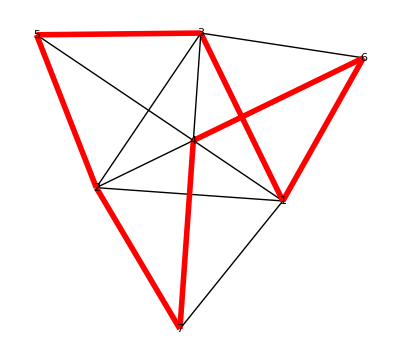
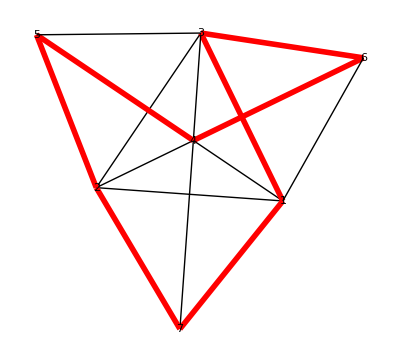
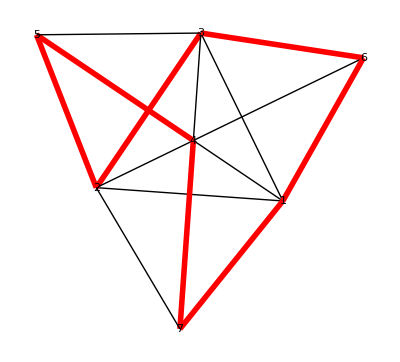
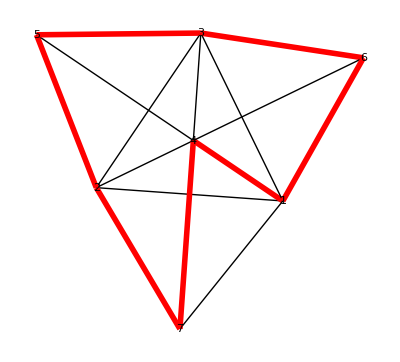
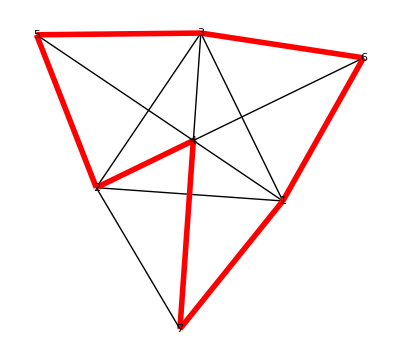
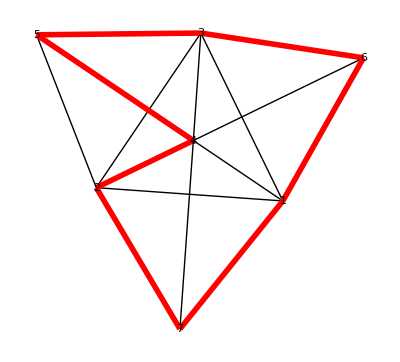
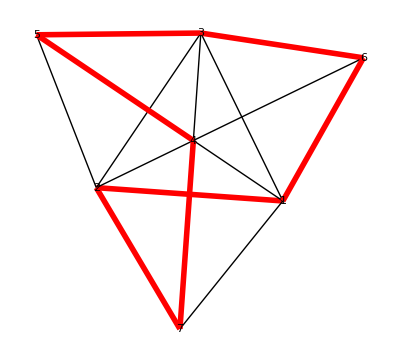
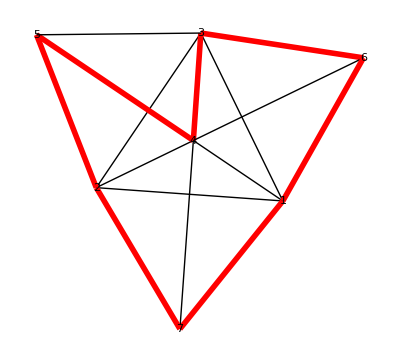
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GraphPlot[g,EdgeRenderingFunction->(If[MemberQ[Transpose[{dd[[i]],RotateRight[dd[[i]]]}],#2]||MemberQ[Transpose[{dd[[i]],RotateRight[dd[[i]]]}],Reverse[#2]],{Red,Thickness[.01],Line[#1]},{Black,Line[#1]}]&),VertexLabeling->True],{i,1,24}]
```

```mathematica
({{1, □, 1, □, 1}, {□, □, □, 1, □}, {□, □, 1, □, 1}, {□, □, □, □, □}, {□, □, □, □, 1}})
```

```mathematica
tf[x_]:=Piecewise[{{1, x==True}, {0, x==False}}]
```

```mathematica
GroupMultiplicationTable[SymmetricGroup[7]]//TableForm
```

```mathematica
A=GroupElements[SymmetricGroup[7]];
```

```mathematica
Table[{i,tf[(PermutationProduct[A[[i]],A[[i]],A[[i]],A[[i]],A[[i]]]==Cycles[{}])&&(A[[i]]!=Cycles[{}])]},{i,1,5040}]
```

```mathematica
FindPermutation[Range[7],{1,7,4,5,2,6,3}]
```

```mathematica
perm=Cycles[{{2,5,4,3,7}}]
```

Cycles[{{2,5,4,3,7}}]

```mathematica
rules[cycle_]:=Thread[DirectedEdge[cycle,RotateLeft[cycle]]];
Flatten[rules/@First[perm]]
```

{2->5,5->4,4->3,3->7,7->2}

```mathematica
Graph[%,VertexLabeling->True,DirectedEdges->True]
```

```mathematica
GraphPlot[{2->5,5->4,4->3,3->7,7->2},VertexLabeling->True,DirectedEdges->True]
```